```mathematica
(* This cell contains generic setup stuff to prepare for execution of the programs *)
ClearAll["Global`*"]; ParamsAreSet = False;
NBDir = SetDirectory[NotebookDirectory[]];
HomeDir = Directory[];
CodeDir = HomeDir<>"/..";
CDToHomeDir := SetDirectory[HomeDir];
CDToCodeDir := SetDirectory[HomeDir<>"/.."];
CDToCodeDir;
<<SetupModelSolutionRoutines.m;
<<SetParamsToBaselineVals.m;
CDToHomeDir;
aGridVecExcBotSmallLength = 20;
aGridVecExcBotLargeLength = 20;
SetupGrids;
SetupShocks;
ConstructLastPeriodAsSmoothedInfHorPFLiqConstrSolnJoinedAtPeriod[3];
```

```mathematica
(* 
Theory tells us that the perfect foresight liquidity constrained solution is an upper bound to the consumption function when uncertainty is present.  This suggests a strategy of approximating the difference between the numerically-solved consumption function and the PFLiq solution.  
*)
```

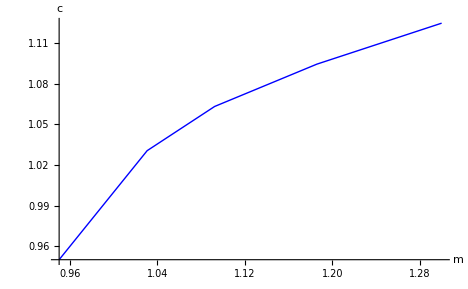

```mathematica
(* Solution to the PFLiq problem *)Plot[{𝒸LinearSplineFunc[[-1]][m]},{m,0.95,1.3},PlotStyle->{Black,Red,Green,Blue},AxesLabel->{"m","c"}]
```

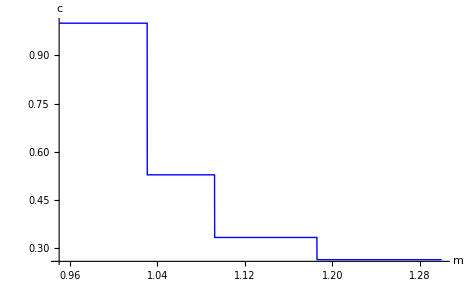

```mathematica
Plot[{𝒸LinearSplineFunc[[-1]]'[m]},{m,0.95,1.3},PlotStyle->{Black,Red,Green,Blue},AxesLabel->{"m","c"}]
```

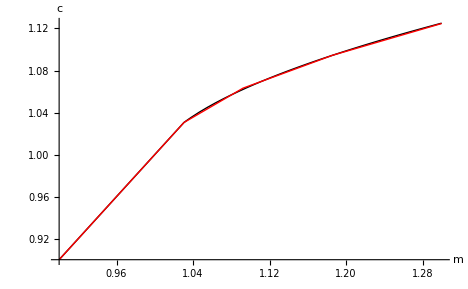

```mathematica
(* 
Problem: the correct consumption function will be smooth; but the PFLiq function is nonsmooth, so the difference will be nonsmooth, which is difficult to approximate.

Solution: Construct a smooth function that is weakly larger than the nonsmooth PFLiq solution.  (That is, it matches at some points and is larger at others).

A natural candidate is the continuous function corresponding to the analytical solution to the liquidity constrained solution.  (See DefineLiqConstrKinkFuncs.m)  This matches the piecewise-linear liquidity constrained function at the kink points, but is larger at values of n between the n kink points.*)

Plot[{cLiqExact[m],𝒸LinearSplineFunc[[-1]][m]},{m,0.9,1.3},PlotStyle->{Black,Red,Green,Blue},AxesLabel->{"m","c"}]
```

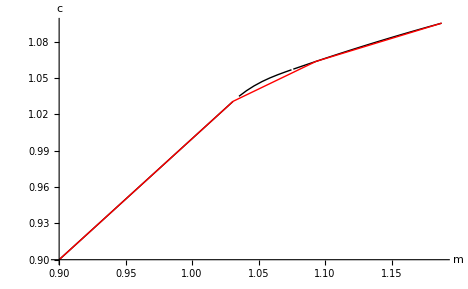

```mathematica
(* This is better, but there's still a kink at the n=0 point; below that point, the MPC κ=1, while above it the MPC is strictly less than 1.  

A simple solution is to construct a function 𝒸Lim that smoothly connects the n=0 point with a point corresponding to some n≥1; this is done in SetupMakeSmoothApproxToLiqConstrSoln[JoinAtNode=3].m; results below *)

Plot[{𝒸Lim[m],𝒸LinearSplineFunc[[-1]][m]},{m,0.9,m♮},PlotStyle->{Black,Red,Green,Blue},AxesLabel->{"m","c"}]
```

```mathematica
(* Using this 𝒸Lim as the limiting function, now solve backwards *)
```

```mathematica
VerboseOutput=True;Do[SolveAnotherPeriod,{10}]
```

Solved 10 periods.

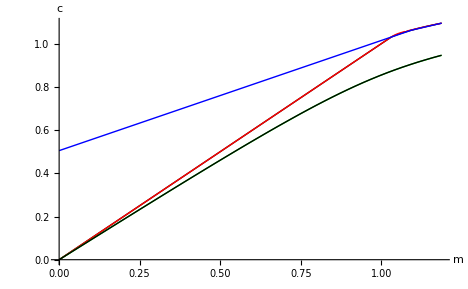

```mathematica
Plot[{cLiqExact[m],𝒸Lim[m],𝒸LinearSplineFunc[[-1]][m],cLiqOrder1Func[m],𝒸[m]},{m,0.,m♮},PlotStyle->{Black,Red,Green,Blue},AxesLabel->{"m","c"}]
```

```mathematica
(* Now examine the MPC for the approximated consumption function in the neighborhood of 1 for the various constructed functions and the approximated consumption function *)
```

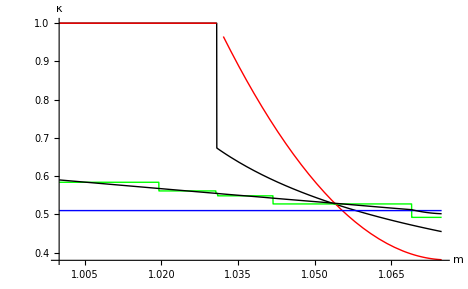

```mathematica
Plot[{κLiqExact[m],κLim[m],𝒸LinearSplineFunc[[-1]]'[m],cLiqOrder1Func'[m],κ[m]},{m,1.0,(*m♮*)mSplice},PlotStyle->{Black,Red,Green,Blue},PlotRange->All,AxesLabel->{"m","κ"}]
```